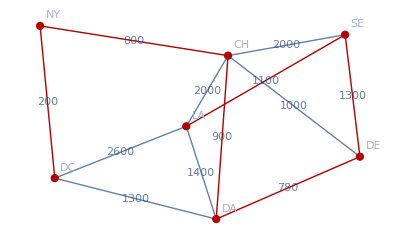

```mathematica
s = SparseArray[{
{1,2}-> 1100, {1,4}-> 1400, {1,5}-> 2000, {1,6} -> 2600,
{2,3}-> 1300,{2,5} ->2000,
{3,4}-> 780, {3,5}->1000,
{4,5}-> 900, {4,6}-> 1300,
{5,7} -> 800,
{6,7} -> 200
}, {7,7}, Infinity];
S = Normal[s];
vertex = {1->"LA",2-> "SE",3-> "DE", 4->"DA",5-> "CH", 6->"DC",7-> "NY"};
gr = WeightedAdjacencyGraph[S,DirectedEdges->False, VertexLabels-> vertex, EdgeLabels->"EdgeWeight"];
sps = FindSpanningTree[gr, EdgeLabels -> "EdgeWeight"];
HighlightGraph[gr, sps]
```

```mathematica
city = Interpreter["City"][{"LA","Seattle","Denver","Dallas","Cicago","Washington DC","NY"}]
```

{Los Angeles,Seattle,Denver,Dallas,Chicago,Washington,New York City}

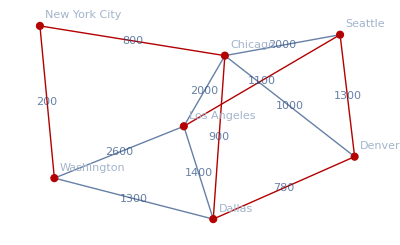

```mathematica
gcity= VertexReplace[gr ,Thread[Range[7]->city],VertexLabels->"Name"];
sps = FindSpanningTree[gcity, EdgeLabels -> "EdgeWeight"];
hg =HighlightGraph[gcity, sps,EdgeStyle->Green]
```

```mathematica
GeoGraphPlot[ hg,
GraphHighlightStyle->"DehighlightGray",
GeoRange->Entity["Country", "UnitedStates"]]
```

-Graphics-

```mathematica
Needs["Combinatorica`"]
$ContextPath
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

{Combinatorica`,SVTools`,Utilities`URLTools`,JLink`,XMPTools`Wrappers`,XMPTools`Helpers`,DocumentationSearch`,ResourceLocator`,System`,Global`}

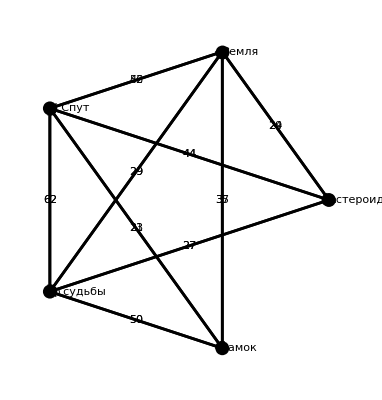

```mathematica
g=({{∞, 52, 29, 35, 29}, {46, ∞, 62, 21, 44}, {29, 62, ∞, 50, 27}, {37, 23, 50, ∞, ∞}, {24, 44, 27, ∞, ∞}});
G= FromAdjacencyMatrix[g,EdgeWeight  ,Type->Directed];
G = SetVertexLabels[G,{"Земля","Ч.Спут","ф.судьбы","замок","астероид"}];
ShowGraph[SetEdgeLabels[G,GetEdgeWeights[G]],EdgeLabelPosition->Center]
```

```mathematica
trail = TravelingSalesman[G]
CostOfPath[G,trail]

GetEdgeWeights[G,Partition[trail,2,1]]
```

{1,3,5,2,4,1}

158

{29,21,27,37,44}

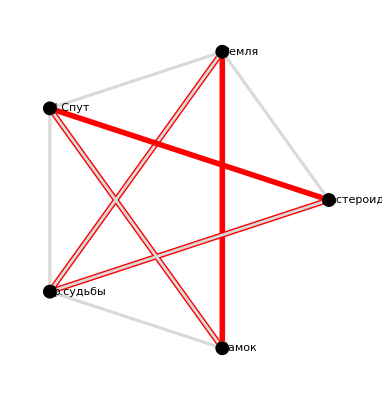

```mathematica
ShowGraph[Highlight[G,{Partition[trail,2,1]},HighlightedEdgeColors->{Red},HighlightedEdgeStyle->Thickness[0.01]],EdgeColor->LightGray]
```

```mathematica
AnimateGraph[G,Prepend[Partition[trail,2,1],1],HighlightedEdgeColors->{Red},HighlightedEdgeStyle->Thickness[0.01],HighlightedVertexStyle->Disk[0.05]]
```

```mathematica
$ContextPath=DeleteCases[$ContextPath,"Combinatorica`"];
$ContextPath
```

{SVTools`,Utilities`URLTools`,JLink`,XMPTools`Wrappers`,XMPTools`Helpers`,DocumentationSearch`,ResourceLocator`,System`,Global`}

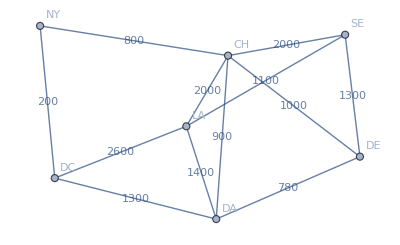

{1100,1400,2000,2600,1300,2000,780,1000,900,1300,800,200}

{{7,6},{6,1}}

{7→6,6→1}

2800

```mathematica
gr
AnnotationValue[gr,EdgeWeight]
Partition[{7,6,1},2,1]
#1->#2&@@@Partition[{7,6,1},2,1]
Total[AnnotationValue[{gr,#1->#2},EdgeWeight]&@@@Partition[{7,6,1},2,1]]
```

```mathematica
CostPath[G_,l_]:=Total[AnnotationValue[{G,#1->#2},EdgeWeight]&@@@Partition[ #,2,1]]&/@l
```

```mathematica
CostPath[gr,{{1,2,3,4},{4,5,7}}]
```

{3180,1700}